## Visualization

## Original

### Variables

```mathematica
theEdgeInCoords = Table[{Green,Thickness[0.003],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,thelines}];
```

```mathematica
theSelectedEdgeInCoords = Table[{Red,Thickness[0.003],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,theSelectedLines}];
```

```mathematica
theBasicBalls=Table[{Opacity[0.5], If[True,degreeColor[theJ⟦i, 2⟧],Brown], Ball[theJ⟦i,4⟧,theJ⟦i,5⟧]},{i,Dimensions[theJ]⟦1⟧}];
```

```mathematica
theMergedBalls:=Function[{theJuncHistory,iter},
	colorByDegree=True;
	Table[{Opacity[0.5], If[colorByDegree,degreeColor[theJuncHistory⟦iter,1,i,2⟧], Blue], Ball[theJuncHistory⟦iter,1,i,4⟧,theJuncHistory⟦iter,1,i,5⟧]},{i,Dimensions[theJuncHistory⟦iter,1⟧]⟦1⟧}]
];
```

```mathematica
mergingBall1[iter_] := {Opacity[0.8], Cyan, Ball[theJuncHistory⟦iter,2,1,4⟧,theJuncHistory⟦iter,2,1,5⟧]};
mergingBall2[iter_] := {Opacity[0.8], Red, Ball[theJuncHistory⟦iter,2,2,4⟧,theJuncHistory⟦iter,2,2,5⟧]};
newMergingBall[iter_] := {Opacity[0.8], Yellow, Ball[theJuncHistory⟦iter,2,3,4⟧,theJuncHistory⟦iter,2,3,5⟧]};
```

```mathematica
Manipulate[{theJuncHistory⟦iter,2,1,2⟧,theJuncHistory⟦iter,2,2,2⟧,theJuncHistory⟦iter,2,3,2⟧},
	{iter,1,Length[theJuncHistory],1}
]
```

### Graphs

```mathematica
Manipulate[Show[Graphics3D[{
Table[{Opacity[0.5], Brown, Ball[Select[theJ, (#⟦5⟧)/(#⟦6⟧)> thres &]⟦i,4⟧,2]},{i,Dimensions[Select[theJ, (#⟦5⟧)/(#⟦6⟧)> thres &]]⟦1⟧}],
theEdgeInCoords
}]],{thres,0,4,0.2}]
```

```mathematica
Manipulate[
	Show[Graphics3D[{
			If[showEdges,theEdgeInCoords],
			If[showSelectedEdges,theSelectedEdgeInCoords],
			(*If[showFullBasicBalls,theFullBasicBalls],*)
			If[showBasicBalls,theBasicBalls],
			
			If[showMergedBalls,theMergedBalls[theJuncHistory,iter]],
			If[showMergingBall1,mergingBall1[iter]],
			If[showMergingBall2,mergingBall2[iter]],
			If[showNewMergingBall,newMergingBall[iter]]
		}]
	],
	{showEdges, {True, False}},
	{showSelectedEdges, {True, False}},
	{showBasicBalls, {True, False}},
	(*{showFullBasicBalls, {True, False}},*)
	{showMergedBalls, {True, False}},
	{showMergingBall1,{True,False}},
	{showMergingBall2,{True,False}},
	{showNewMergingBall,{True,False}},
	{iter,1,Length[theJuncHistory],1}
	
]
```

### Histogram

```mathematica
Manipulate[Histogram[theJuncHistory⟦iter,1,;;,2⟧,{1,16,1}],{iter,1,Length[theJuncHistory],1}]
```

## Dilation

### Variables

```mathematica
dEdgeInCoords = Table[{Green,Thickness[0.003],Line[{dPoints⟦skelLine⟦1⟧⟧,dPoints⟦skelLine⟦2⟧⟧}]},{skelLine,dLines}];
```

```mathematica
dSelectedEdgeInCoords = Table[{Red,Thickness[0.003],Line[{dPoints⟦skelLine⟦1⟧⟧,dPoints⟦skelLine⟦2⟧⟧}]},{skelLine,dSelectedLines}];
```

```mathematica
dBasicBalls=Table[{Opacity[0.5], If[True,degreeColor[dJ⟦i, 2⟧],Brown], Ball[dJ⟦i,4⟧,dJ⟦i,5⟧]},{i,Dimensions[dJ]⟦1⟧}];
```

```mathematica
dMergedBalls:=Function[{theJuncHistory,iter},
	colorByDegree=True;
	Table[{Opacity[0.5], If[colorByDegree,degreeColor[theJuncHistory⟦iter,1,i,2⟧], Blue], Ball[theJuncHistory⟦iter,1,i,4⟧,theJuncHistory⟦iter,1,i,5⟧]},{i,Dimensions[theJuncHistory⟦iter,1⟧]⟦1⟧}]
];
```

```mathematica
dFinalBalls=Table[{Opacity[0.5], If[True,degreeColor[dJres⟦i, 2⟧],Brown], Ball[dJres⟦i,4⟧,dJres⟦i,5⟧]},{i,Dimensions[dJres]⟦1⟧}];
```

```mathematica
dMergingBall1[iter_] := {Opacity[0.8], Cyan, Ball[dJuncHistory⟦iter,2,1,4⟧,dJuncHistory⟦iter,2,1,5⟧]};
dMergingBall2[iter_] := {Opacity[0.8], Red, Ball[dJuncHistory⟦iter,2,2,4⟧,dJuncHistory⟦iter,2,2,5⟧]};
dNewMergingBall[iter_] := {Opacity[0.8], Yellow, Ball[dJuncHistory⟦iter,2,3,4⟧,dJuncHistory⟦iter,2,3,5⟧]};
```

```mathematica
Manipulate[{dJuncHistory⟦iter,2,1,2⟧,dJuncHistory⟦iter,2,2,2⟧,dJuncHistory⟦iter,2,3,2⟧},
	{iter,1,Length[dJuncHistory],1}
]
```

### Graphs

```mathematica
Manipulate[Show[Graphics3D[{
Table[{Opacity[0.5], Brown, Ball[Select[dJ, #⟦5⟧> thres &]⟦i,4⟧,2]},{i,Dimensions[Select[dJ, #⟦5⟧ > thres &]]⟦1⟧}],
dEdgeInCoords
}]],{thres,0,4,0.2}]
```

```mathematica
Manipulate[
	Show[Graphics3D[{
			If[showEdges,dEdgeInCoords],
			If[showSelectedEdges,dSelectedEdgeInCoords],
			(*If[showFullBasicBalls,theFullBasicBalls],*)
			If[showBasicBalls,dBasicBalls],
			If[showMergedBalls,dMergedBalls[dJuncHistory,iter]],
			If[showFinalBalls,dFinalBalls],
			If[showMergingBall1,dMergingBall1[iter]],
			If[showMergingBall2,dMergingBall2[iter]],
			If[showNewMergingBall,dNewMergingBall[iter]]
		}]
	],
	{showEdges, {True, False}},
	{showSelectedEdges, {True, False}},
	{showBasicBalls, {True, False}},
	(*{showFullBasicBalls, {True, False}},*)
	{showMergedBalls, {True, False}},
	{showFinalBalls, {True, False}},
	{showMergingBall1,{True,False}},
	{showMergingBall2,{True,False}},
	{showNewMergingBall,{True,False}},
	{iter,1,Length[dJuncHistory],1}
	
]
```

### Histogram

```mathematica
Manipulate[Histogram[dJuncHistory⟦iter,1,;;,2⟧,{1,16,1}],{iter,1,Length[dJuncHistory],1}]
```

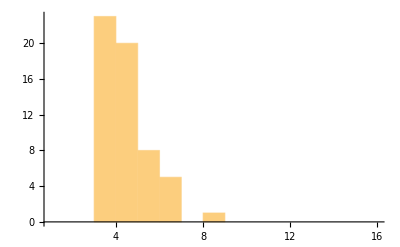

```mathematica
Histogram[dJres⟦;;,2⟧,{1,16,1}]
```